```mathematica
<<mf23.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];(* this division by cf might spoil interpolation *)
Return[collect2]]
```

```mathematica
For[m=2,m<5,m++;
Print[jNew[5,m]];
Print[test[5,m]]]
```

744+1/x+196884 x+21493760 x^2+864299970 x^3

744+1/x+196884 x+21493760 x^2+864299970 x^3

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

```mathematica
For[m=2,m<5,m++;
jn=jNew[5,m];
Print["m ",m];
Print[jn]]
```

m 3

744+1/x+196884 x+21493760 x^2+864299970 x^3

m 4

1664+1/x+1119232 x+394264576 x^2+81264771072 x^3

m 5

3160+1/x+4287700 x+3316992000 x^2+1669770821250 x^3

```mathematica
stream=OpenWrite["run14sept20no1"];
For[m=2,m<302,m++;
jay=jNew[100,m];
Write[stream,{m,jay}]];
Close[stream]
```

run14sept20no1

```mathematica
notA2Q[z_]:=Module[{tf},
tf=True;
If[Abs[z]==2,tf=False];
Return[tf]]
```

```mathematica
nonzeroQ[z_]:=Module[{tf},
tf=True;
If[z==0,tf=False];
Return[tf]]
```

```mathematica
realQ[z_]:=Module[{tf},
tf=False;
If[Im[z]==0,tf=True];
Return[tf]]
```

```mathematica
imaginaryQ[z_]:=Module[{tf},
tf=False;
If[Re[z]==0,tf=True];
Return[tf]]
```

```mathematica
listRoots2[poly_,x_,precision_]:=Module[{sl,solv,rt,at,roots},
sl=Solve[poly==0,x];
solv=secondmap[firstmap[sl]];
rt=reset[solv];
at=imset[solv];
roots=rt+I*at;
Return[N[roots,precision]]]
```

```mathematica
argPrincipleCircleContour3[f_,center_,radius_,precision_,accuracy_]:=
Module[{gamma,g,hh,int,number},
gamma[t_]:=center+Exp[t*I]*radius;
g[t_]:=f'[t]/f[t];
hh[t_]:=g[gamma[t]]*gamma'[t];
int=NIntegrate[hh[t],{t,0,2*Pi}, WorkingPrecision->precision,AccuracyGoal->accuracy]/(2*Pi*I);
number=Round[int];
Return[number]]
```

```mathematica
stream=OpenWrite["run28jun20no4"];
For[m=2,m<102,m++;
jay=jNew[25,m];
Write[stream,{m,jay}]];
Close[stream]
```

run28jun20no4

```mathematica
rstream=OpenRead["run28jun20no4"];
list=ReadList[rstream];
Close[rstream];
Length[list]
```

100

=======================================================

zeros of polynomial interpolating the coefficient of x^2

length of data file 99

degree of interpolating polynomial = 9

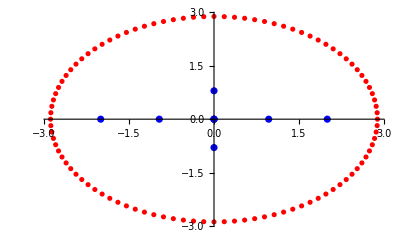

root count,real root count,imaginary root count

{6,4,2}

radius: 2.88539

(maximum modulus)(log d)/d ~ 0.3346

=======================================================

zeros of polynomial interpolating the coefficient of x^3

length of data file 99

degree of interpolating polynomial = 12

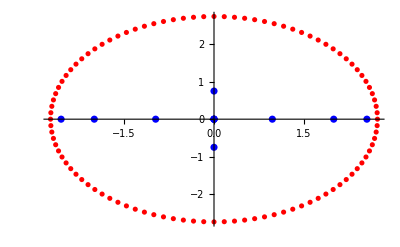

root count,real root count,imaginary root count

{8,6,2}

radius: 2.73072

(maximum modulus)(log d)/d ~ 0.93538

=======================================================

zeros of polynomial interpolating the coefficient of x^4

length of data file 99

degree of interpolating polynomial = 15

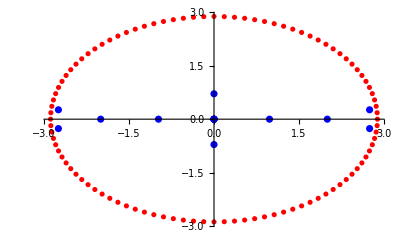

root count,real root count,imaginary root count

{10,4,2}

radius: 2.88539

(maximum modulus)(log d)/d ~ 0.95624

=======================================================

zeros of polynomial interpolating the coefficient of x^5

length of data file 99

degree of interpolating polynomial = 18

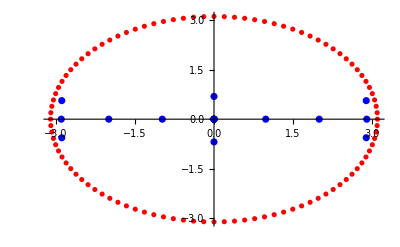

root count,real root count,imaginary root count

{12,6,2}

radius: 3.10667

(maximum modulus)(log d)/d ~ 0.94862

=======================================================

zeros of polynomial interpolating the coefficient of x^6

length of data file 99

degree of interpolating polynomial = 21

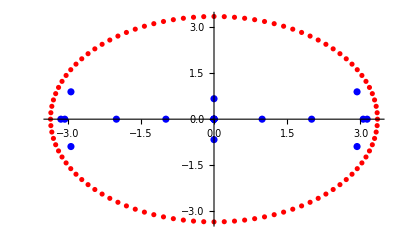

root count,real root count,imaginary root count

{14,8,2}

radius: 3.34866

(maximum modulus)(log d)/d ~ 0.93689

=======================================================

zeros of polynomial interpolating the coefficient of x^7

length of data file 99

degree of interpolating polynomial = 24

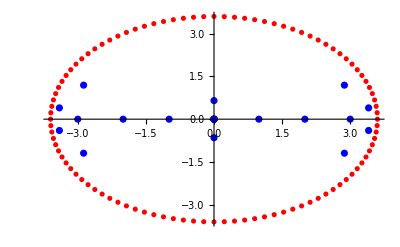

root count,real root count,imaginary root count

{16,6,2}

radius: 3.59729

(maximum modulus)(log d)/d ~ 0.95223

=======================================================

zeros of polynomial interpolating the coefficient of x^8

length of data file 99

degree of interpolating polynomial = 27

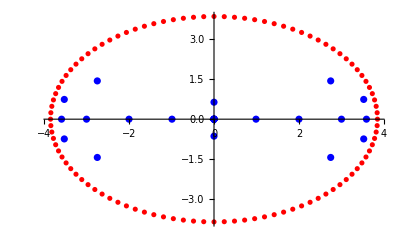

root count,real root count,imaginary root count

{18,8,2}

radius: 3.84719

(maximum modulus)(log d)/d ~ 0.93582

=======================================================

zeros of polynomial interpolating the coefficient of x^9

length of data file 99

degree of interpolating polynomial = 30

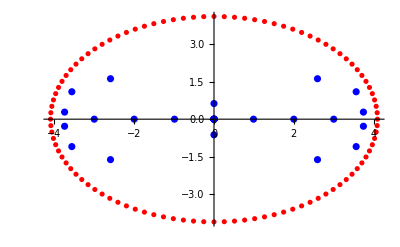

root count,real root count,imaginary root count

{20,6,2}

radius: 4.09608

(maximum modulus)(log d)/d ~ 0.91659

=======================================================

zeros of polynomial interpolating the coefficient of x^10

length of data file 99

degree of interpolating polynomial = 33

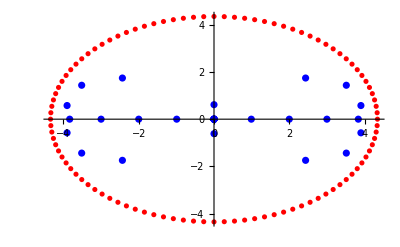

root count,real root count,imaginary root count

{22,8,2}

radius: 4.34294

(maximum modulus)(log d)/d ~ 0.90856

=======================================================

zeros of polynomial interpolating the coefficient of x^11

length of data file 99

degree of interpolating polynomial = 36

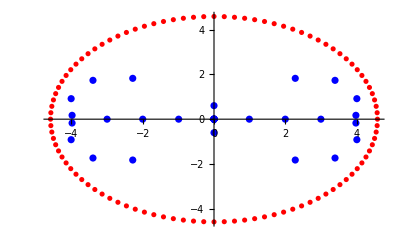

root count,real root count,imaginary root count

{24,6,2}

radius: 4.58736

(maximum modulus)(log d)/d ~ 0.89645

=======================================================

zeros of polynomial interpolating the coefficient of x^12

length of data file 99

degree of interpolating polynomial = 39

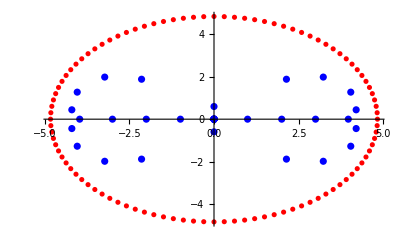

root count,real root count,imaginary root count

{26,8,2}

radius: 4.82916

(maximum modulus)(log d)/d ~ 0.87714

=======================================================

zeros of polynomial interpolating the coefficient of x^13

length of data file 99

degree of interpolating polynomial = 42

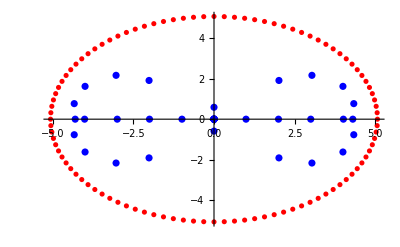

root count,real root count,imaginary root count

{28,10,2}

radius: 5.06833

(maximum modulus)(log d)/d ~ 0.86839

=======================================================

zeros of polynomial interpolating the coefficient of x^14

length of data file 99

degree of interpolating polynomial = 45

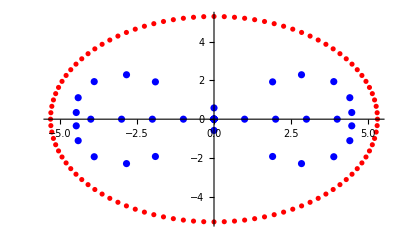

root count,real root count,imaginary root count

{30,8,2}

radius: 5.30492

(maximum modulus)(log d)/d ~ 0.8568

=======================================================

zeros of polynomial interpolating the coefficient of x^15

length of data file 99

degree of interpolating polynomial = 48

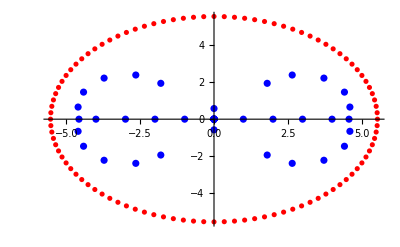

root count,real root count,imaginary root count

{32,10,2}

radius: 5.53904

(maximum modulus)(log d)/d ~ 0.84037

=======================================================

zeros of polynomial interpolating the coefficient of x^16

length of data file 99

degree of interpolating polynomial = 51

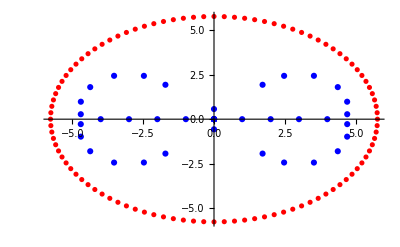

root count,real root count,imaginary root count

{34,8,2}

radius: 5.77078

(maximum modulus)(log d)/d ~ 0.83212

=======================================================

zeros of polynomial interpolating the coefficient of x^17

length of data file 99

degree of interpolating polynomial = 54

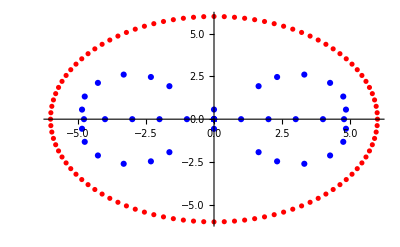

root count,real root count,imaginary root count

{36,10,2}

radius: 6.00025

(maximum modulus)(log d)/d ~ 0.82094

=======================================================

zeros of polynomial interpolating the coefficient of x^18

length of data file 99

degree of interpolating polynomial = 57

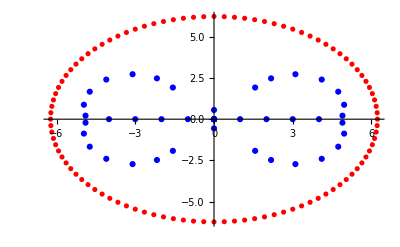

root count,real root count,imaginary root count

{38,8,2}

radius: 6.22757

(maximum modulus)(log d)/d ~ 0.80838

=======================================================

zeros of polynomial interpolating the coefficient of x^19

length of data file 99

degree of interpolating polynomial = 60

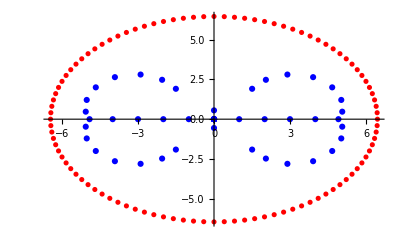

root count,real root count,imaginary root count

{40,10,2}

radius: 6.45284

(maximum modulus)(log d)/d ~ 0.80084

=======================================================

zeros of polynomial interpolating the coefficient of x^20

length of data file 99

degree of interpolating polynomial = 63

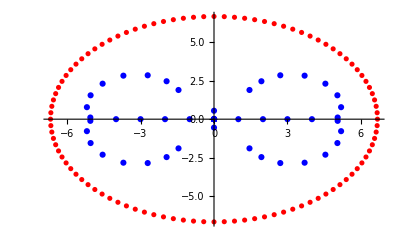

root count,real root count,imaginary root count

{42,8,2}

radius: 6.67616

(maximum modulus)(log d)/d ~ 0.78987

=======================================================

zeros of polynomial interpolating the coefficient of x^21

length of data file 99

degree of interpolating polynomial = 66

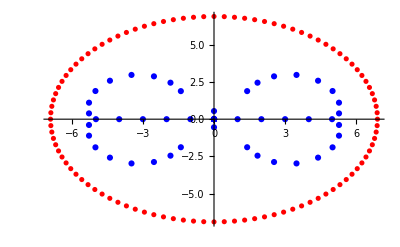

root count,real root count,imaginary root count

{44,10,2}

radius: 6.89763

(maximum modulus)(log d)/d ~ 0.78131

=======================================================

zeros of polynomial interpolating the coefficient of x^22

length of data file 99

degree of interpolating polynomial = 69

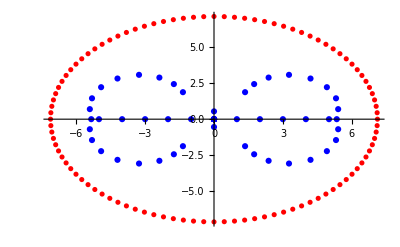

root count,real root count,imaginary root count

{46,12,2}

radius: 7.11734

(maximum modulus)(log d)/d ~ 0.77355

=======================================================

zeros of polynomial interpolating the coefficient of x^23

length of data file 99

degree of interpolating polynomial = 72

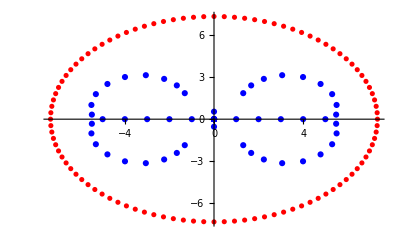

root count,real root count,imaginary root count

{48,10,2}

radius: 7.33537

(maximum modulus)(log d)/d ~ 0.7628

**************************************************************

max (roots)log(d)/d) vs. d

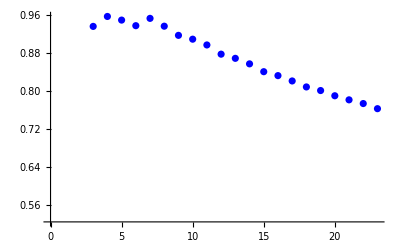

degrees

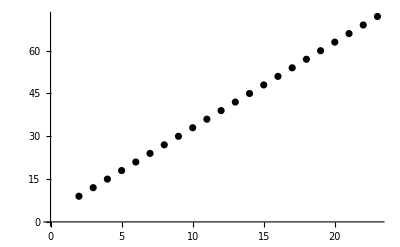

number of impure roots plot

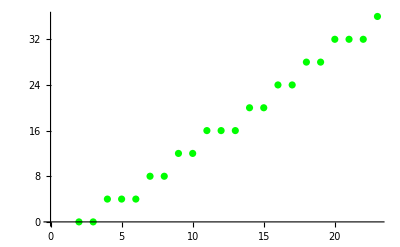

run26mar21no12

```mathematica
rstream=OpenRead["run28jun20no4"];
list=ReadList[rstream];
Close[rstream];
wstream1=OpenWrite["run26mar21no12"];
maxes={};
centers={};
degrees={};
impurenumber={};
precision=100;
truncation=23;
pointsize=.01;
color=Blue;


For[d=1,d<truncation,d++;
radius=d/Log[d];
circle={};
For[a=-1,a<99,a++;
theta=(a/100)*2*Pi;
point={radius*Cos[theta],radius*Sin[theta]};
circle=AppendTo[circle,point]
]; (* a *)


data={};
Print["======================================================="];
Print["zeros of polynomial interpolating the coefficient of x^",d];
For[k=0,k<99,k++;
m=list[[k,1]];
srs=list[[k,2]];
srs2=Normal[Series[srs,{x,0,truncation}]];
c=Coefficient[srs2,x,d];
data=Append[data,{m,c}];
] (* k loop *);
Print["length of data file ",Length[data]];
ip=Collect[InterpolatingPolynomial[data,x],x];
degree=Exponent[ip,x];
Print["degree of interpolating polynomial = ",degree];
AppendTo[degrees,{d,degree}];
fr=findRoots[ip,x];
lpr=ListPlot[fr,PlotStyle->Blue];
cpr=ListPlot[circle,PlotStyle->Red];
Print[Show[lpr,cpr,PlotRange->All]];
roots=listRoots2[ip,x,precision];
roots=Select[roots,nonzeroQ];
rootsnumber=Length[roots];
realroots=Select[roots,realQ];
realrootsnumber=Length[realroots];
imaginaryroots=Select[roots,imaginaryQ];
imaginaryrootsnumber=Length[imaginaryroots];
Print["root count,real root count,imaginary root count"];
Print[{rootsnumber,realrootsnumber,imaginaryrootsnumber}];
AppendTo[impurenumber,{d,rootsnumber-realrootsnumber-imaginaryrootsnumber}];
pRoots=Select[roots,notA2Q];
max=Max[Abs[pRoots]*Log[d]/d];
Print["radius: ",N[radius]];
Print["(maximum modulus)(log d)/d ~ ",N[max,5]];
Write[wstream1,{d,ip,roots,max}];
AppendTo[maxes,{d,max}]];
Print["**************************************************************"];
Print["max (roots)log(d)/d) vs. d"];
Print[ListPlot[maxes,PlotStyle->Blue]];
Print["degrees"];
Print[ListPlot[degrees,PlotStyle->Black]];
Print["number of impure roots plot"];
Print[ListPlot[impurenumber,PlotStyle->Green]];
Close[wstream1]
```